# Thesis Project: Cement Hydrates C-H-S 400K

## K-Points Analysis DFTB+

### Working directory and Figures directory

```mathematica
wrkdir = "/home/qbit/Documents/git-repositories/bachelor-thesis/cluster-files/";
SetDirectory[wrkdir];
```

```mathematica
figDir="/home/qbit/Documents/git-repositories/bachelor-thesis/figures/"
```

/home/qbit/Documents/git-repositories/bachelor-thesis/figures/

### The k-point grid

```mathematica
bulk = Import["../dftb/eos/POSCAR-init", "Table"];
```

```mathematica
lattbulk = bulk[[2, 1]] bulk[[3;;5]]
```

{{13.5354,0.18446,0.00755401},{-16.2629,24.8887,-0.00875423},{0.543338,-0.483321,23.4374}}

```mathematica
{a, b, c} = lattbulk;
```

```mathematica
Δk = Table[0.07-0.005 i, {i, 0, 10}];
```

```mathematica
Δk//Map[{#, Round[((b×c)/((a×b).c)//Norm)/#],
Round[((c×a)/((a×b).c)//Norm)/#],
Round[((a×b)/((a×b).c)//Norm)/#]}&, #]&//TableForm
```

0.07 | 1 | 1 | 1
0.065 | 1 | 1 | 1
0.06 | 1 | 1 | 1
0.055 | 2 | 1 | 1
0.05 | 2 | 1 | 1
0.045 | 2 | 1 | 1
0.04 | 2 | 1 | 1
0.035 | 2 | 1 | 1
0.03 | 3 | 1 | 1
0.025 | 3 | 2 | 2
0.02 | 4 | 2 | 2

We will run the xkp.sh script for k-points densities 0.06, 0.04, and 0.03

### Convergency of k-points

```mathematica
data = Import["../dftb/kp.dat"]
```

{{1,-4660.48,43},{2,-4660.51,58},{3,-4660.51,37}}

```mathematica
kpdat =data[[All,{1,2}]]//Map[#/{1,690}&]
```

{{1,-6.75432},{2,-6.75437},{3,-6.75436}}

#### Get the x and y data:

```mathematica
kpY=kpdat[[All,2]]
kpX={0.06,0.04,0.03}
```

{-6.75432,-6.75437,-6.75436}

{0.06,0.04,0.03}

#### Plot the data:

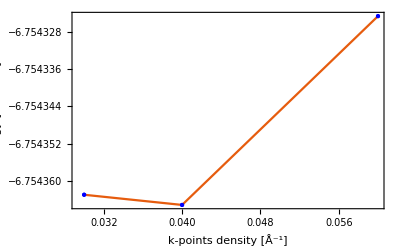

```mathematica
kpPlotNoWindow=ListPlot[
Transpose[{kpX,kpY}],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Blue]},
Frame->True,
FrameLabel->
{"k-points density [Å^-1]", "Energy [eV/atom]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400]
```

```mathematica
Export[FileNameJoin[{figDir,"kp-dftb-nw.png"}], kpPlotNoWindow, ImageResolution->300];
```

#### Let’s analyse the convergency of these data using the 1 meV/atom criteria

```mathematica
energyMin=kpdat[[1,2]]+10^-3/2;
energyMax=kpdat[[1,2]]-10^-3/2;
```

```mathematica
kPlot=ListPlot[
Transpose[{kpX,kpY}],
PlotRange->{kpdat[[1,2]]+10^-3, kpdat[[1,2]]-10^-3},
PlotTheme->"Scientific",
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Blue]},
Frame->True,
FrameLabel->
{"k-points density [Å^-1]", "Energy [eV/atom]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400];
```

```mathematica
energyWindow=Graphics[{(*Shaded rectangle*){Gray,Opacity[0.3],Rectangle[{0.02,energyMin},{0.07,energyMax}]},(*Dashed lines for rectangle edges*){Dashed,Black,Line[{{0.02,energyMin},{0.07,energyMin}}]},{Dashed,Black,Line[{{0.02,energyMax},{0.07,energyMax}}]},(*Double-headed arrow with annotation*){Arrowheads[{-0.02,0.02}],Arrow[{{0.05,energyMin},{0.05,energyMax}}]},Text[Style["1 meV",FontSize->12,Black],{0.053,0.0001+Mean[{energyMin,energyMax}]}]}];
```

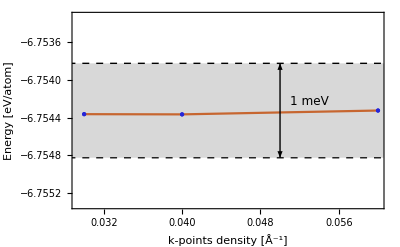

```mathematica
kpPlotWindow =Show[kPlot, energyWindow]
```

```mathematica
Export[FileNameJoin[{figDir,"kp-dftb-w.png"}], kpPlotWindow, ImageResolution->300];
```

From this result, we use from now on the k-point grid 1x1x1

## Cut-off Energy Analysis VASP

### ENCUT

```mathematica
datacem = Import["../dftb/ecut.dat"];
```

```mathematica
dataecut=datacem[[All,{1,2}]]//Map[#/{1,690}&];
```

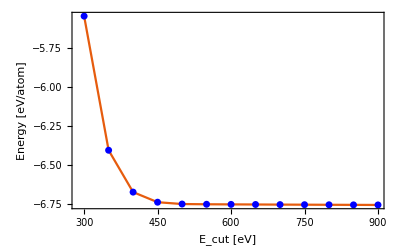

```mathematica
encutPlotNoWindow= dataecut//ListPlot[#,
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"E_cut [eV]","Energy [eV/atom]" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Blue, AbsolutePointSize[5],
Point[#]}
]&
```

```mathematica
Export[FileNameJoin[{figDir,"encut-nw.png"}], encutPlotNoWindow, ImageResolution->300];
```

```mathematica
encutMin=dataecut[[13,2]];
encutMax=dataecut[[13,2]]+10^-3;
```

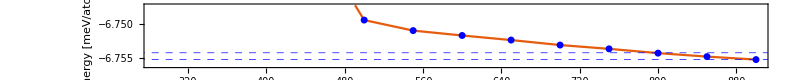

```mathematica
encutPlot =dataecut//ListPlot[#,
PlotTheme->"Scientific",
(*GridLines->Automatic,*)
Frame->True,
FrameLabel->{"E_cut [eV]","Energy [meV/atom]" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->15},
Joined->True,
PlotRange->{#[[-1,2]]-1 10^-3,#[[-1,2]]+8 10^-3},(*{{350,950},{dataecut[[13,2]], dataecut[[2,2]]}},*)
InterpolationOrder->1,
(*ImageSize->400,*)
Epilog->{Blue, AbsolutePointSize[5],
Point[#]},
AspectRatio->0.1,
GridLines->{None,{#[[-1,2]],#[[-1,2]]+10^-3}},
GridLinesStyle->Directive[Blue, Dashed],
ImageSize->800
]&
```

```mathematica
encutWindow=Graphics[{(*Shaded rectangle*){Gray,Opacity[0.3],Rectangle[{200,encutMin},{950,encutMax}]},(*Dashed lines for rectangle edges*){Dashed,Black,Line[{{200,encutMin},{950,encutMin}}]},{Dashed,Black,Line[{{200,encutMax},{950,encutMax}}]},(*Double-headed arrow with annotation*){Arrowheads[{-0.02,0.02}],Arrow[{{750,encutMin},{750,encutMax}}]},Text[Style["1 meV",FontSize->12,Black],{800,Mean[{encutMin,encutMax}]}]}];
```

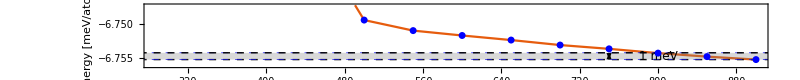

```mathematica
encutPlotWindow=Show[encutPlot,encutWindow]
```

We  use 800 meV for  CSH analysis from now on.

```mathematica
Export[FileNameJoin[{figDir,"encut-w.png"}], encutPlotWindow, ImageResolution->300];
```

## K-Points Analysis VASP

```mathematica
kpDataVasp=Import["kp.dat"][[All, {1,2}]]//Map[#/{1,690}&]
```

{{1,-6.75432},{2,-6.75437},{3,-6.75436}}

```mathematica
kpDataVasp[[All, 2]]
```

{-6.75432,-6.75437,-6.75436}

```mathematica
kPlotVaspNw = ListPlot[
Transpose[{kpX,kpDataVasp[[All, 2]]}],
PlotTheme->"Scientific",
PlotRange->All,
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Blue]},
Frame->True,
FrameLabel->
{"k-points density [Å^-1]", "Energy [eV/atom]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400]
```

-Graphics-

```mathematica
Export[FileNameJoin[{figDir,"kp-vasp-nw.png"}], kPlotVaspNw, ImageResolution->300];
```

```mathematica
energyMinVasp=kpDataVasp[[1,2]]+10^-3/2;
energyMaxVasp=kpDataVasp[[1,2]]-10^-3/2;
```

```mathematica
kPlotVasp=ListPlot[
Transpose[{kpX,kpDataVasp[[All, 2]]}],
PlotRange->{kpDataVasp[[1,2]]+10^-3, kpDataVasp[[1,2]]-10^-3},
PlotTheme->"Scientific",
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Blue]},
Frame->True,
FrameLabel->
{"k-points density [Å^-1]", "Energy [eV/atom]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400];
```

```mathematica
energyWindowVasp=Graphics[{(*Shaded rectangle*){Gray,Opacity[0.3],Rectangle[{0.02,energyMinVasp},{0.07,energyMaxVasp}]},(*Dashed lines for rectangle edges*){Dashed,Black,Line[{{0.02,energyMinVasp},{0.07,energyMinVasp}}]},{Dashed,Black,Line[{{0.02,energyMaxVasp},{0.07,energyMaxVasp}}]},(*Double-headed arrow with annotation*){Arrowheads[{-0.02,0.02}],Arrow[{{0.05,energyMinVasp},{0.05,energyMaxVasp}}]},Text[Style["1 meV",FontSize->12,Black],{0.053,0.0001+Mean[{energyMinVasp,energyMaxVasp}]}]}];
```

```mathematica
kPlotVaspW=Show[kPlotVasp, energyWindowVasp]
```

-Graphics-

```mathematica
Export[FileNameJoin[{figDir,"kp-vasp-w.png"}], kPlotVaspW, ImageResolution->300];
```

## Density of States

```mathematica
pdosData=Import["DOSCAR-cem1.sto", "Table"];
```

```mathematica
Dimensions[pdosData]
```

{2074387}

```mathematica
dos = pdosData[[7;;7+3000]][[All, {1, 2}]];
```

```mathematica
ef = pdosData[[6, 4]]
```

3.069

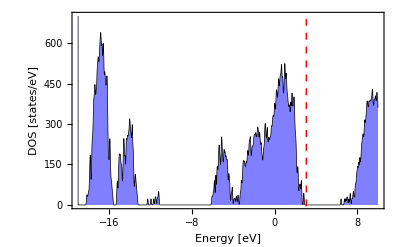

```mathematica
ListPlot[dos, 
PlotTheme->"Scientific",
Joined->True,
Axes->False,
Frame->True,
FrameLabel->
{"Energy [eV]", 
"DOS [states/eV]"},
GridLines->{{ef}, None},
GridLinesStyle-> 
Directive[Red, Dashed,
AbsoluteThickness[1]],
BaseStyle->
{FontFamily->"Helvetica",
FontSize->15},
Filling->Axis,
FillingStyle->
Directive[Opacity[0.5], Blue],
PlotStyle-> 
{AbsoluteThickness[0.5], Black},
ImageSize->400,
PlotRange->{All, {0, 700}}]
```

### Partial Density of States PDOS

Let us define the number of atoms of each element.

```mathematica
atomsCa=99;
atomsSi=60;
atomsO=323;
atomsH=208;
```

## Benchmark

```mathematica
benchRes=Import["results.dat"]
```

{{1,552.512},{2,308.492},{3,235.218},{5,186.864},{7,213.865},{9,187.9},{11,228.094}}

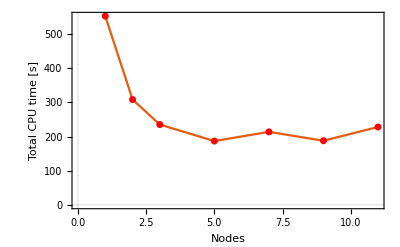

```mathematica
ListPlot[benchRes,
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"Nodes","Total CPU time [s]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Joined->True,InterpolationOrder->1,ImageSize->400,
Epilog->{Red,AbsolutePointSize[5],Point[benchRes]}]
```

```mathematica
benchRes[[All,1]];
```

```mathematica
scaleTCPU=benchRes//Map[#/{1,benchRes[[1,2]]}&];
```

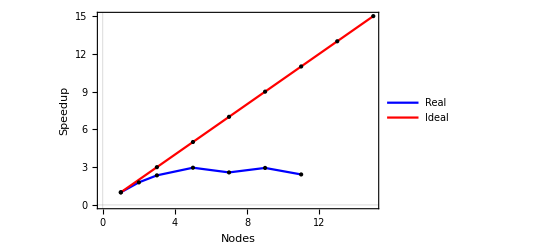

```mathematica
ListPlot[{
Transpose[{scaleTCPU[[All,1]],1/scaleTCPU[[All,2]]}],
Transpose[{Range[1,15,2], Range[1,15,2]}]},
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"Nodes","Speedup"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Joined->True,InterpolationOrder->1,ImageSize->400,
PlotStyle->{Blue, Red},
PlotLegends->Placed[{"Real", "Ideal"} ,After],
Mesh->All,
MeshStyle->
{Directive[PointSize[Medium], Black]}]
```

In light of these results, we will set our maximum number of cores to 4, since there is no speedup for a larger number of cores.

## MLFF Results Analysis (Training)

```mathematica
wrkdir = "/home/qbit/Documents/git-repositories/bachelor-thesis/cluster-files/ml-400k/training/";
SetDirectory[wrkdir];
```

### Optimal Volume

```mathematica
optVolumeTraining=Import["volume.dat"][[All,1]];
```

```mathematica
timeData=2/10^3 Range[0,50000-1]; (*In ps*)
```

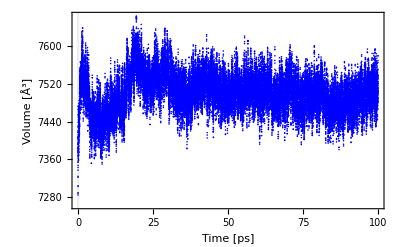

```mathematica
optVolPlotT=ListPlot[
Transpose[{timeData,optVolumeTraining}],
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"Time [ps]","Volume [Å^3]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Joined->False,
PlotRange->All,PlotStyle->Blue,
ImageSize->400]
```

```mathematica
Export[FileNameJoin[{figDir,"opt-vol-t.png"}], optVolPlotT, ImageResolution->300];
```

### Total Energy

```mathematica
totEnergyT=Import["entot.dat"][[All,1]];
```

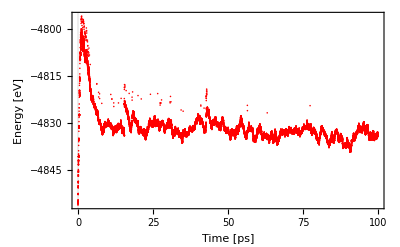

```mathematica
totEnergyPlotT=ListPlot[
Transpose[{timeData,totEnergyT}],
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"Time [ps]","Energy [eV]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Joined->False,
PlotRange->All,PlotStyle->Red,
ImageSize->400]
```

```mathematica
Export[FileNameJoin[{figDir,"toten-t.png"}],totEnergyPlotT, ImageResolution->300];
```

### BEEF & ERR

Get the beef and err data from the ML_LOGFILE from the training process

```mathematica
Run["grep 'BEEF' ML_LOGFILE | tail -n +15 | awk '{print $2\"   \"$4}' > beef.dat"];
```

```mathematica
beefDataT = Import["beef.dat"];
```

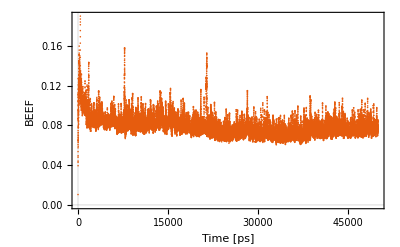

```mathematica
beefPlotT=beefDataT//ListPlot[#,PlotRange->All,
PlotTheme->"Scientific",
Frame->True,
Joined->False,
FrameLabel->{"Time [ps]","BEEF"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400]&
```

```mathematica
Export[FileNameJoin[{figDir,"beef-t.png"}], beefPlotT, ImageResolution->300];
```

## MLFF Results Analysis (Prediction)

```mathematica
wrkdir = "/home/qbit/Documents/git-repositories/bachelor-thesis/cluster-files/ml-400k/prediction/";
SetDirectory[wrkdir];
```

### Optimal Volume

```mathematica
optVolumePredict=Import["volume.dat"][[All,1]];
```

```mathematica
timeDataPredict=2/10^3 Range[0,47858-1]; (*In ps*)
```

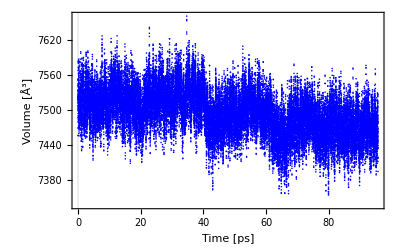

```mathematica
optVolPlotP=ListPlot[
Transpose[{timeDataPredict,optVolumePredict}],
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"Time [ps]","Volume [Å^3]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Joined->False,
PlotRange->All,PlotStyle->Blue,
ImageSize->400]
```

```mathematica
Export[FileNameJoin[{figDir,"opt-vol-p.png"}], optVolPlotP, ImageResolution->300];
```

### Total Energy

```mathematica
totEnergyP=Import["entot.dat"][[All,1]];
```

```mathematica
totEnergyP[[1]]
```

-4833.03

```mathematica
dat=Transpose[{timeDataPredict,totEnergyP}];
```

```mathematica
dat[[-1]]
```

{47857/500,-4837.18}

```mathematica
Sort[{{a,2},{c,1},{d,3}},#1[[2]]<#2[[2]]&]
```

{{{0.543338,-0.483321,23.4374},1},{{13.5354,0.18446,0.00755401},2},{d,3}}

```mathematica
dat//Sort[#,#1[[2]]<#2[[2]]&]&;
```

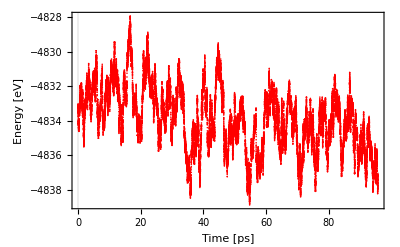

```mathematica
totEnergyPlotP=ListPlot[
Transpose[{timeDataPredict,totEnergyP}],
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"Time [ps]","Energy [eV]"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Joined->False,
PlotRange->All,PlotStyle->Red,
ImageSize->400]
```

```mathematica
Export[FileNameJoin[{figDir,"toten-p.png"}],totEnergyPlotP, ImageResolution->300];
```

### BEEF & ERR

Get the beef and err data from the ML_LOGFILE from the training process

```mathematica
Run["grep 'BEEF' ML_LOGFILE | tail -n +15 | awk '{print $2\"   \"$4}' > beef.dat"];
```

```mathematica
beefData = Import["beef.dat"];
```

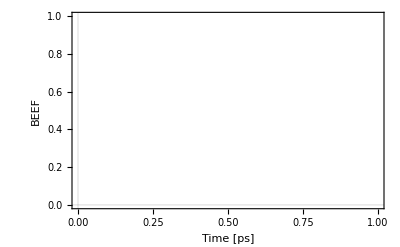

```mathematica
beefData//ListPlot[#,PlotRange->All,
PlotTheme->"Scientific",
Frame->True,
Joined->False,
FrameLabel->{"Time [ps]","BEEF"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400]&
```

## RMSE Energy, Force & Stress

### TOTAL ENERGY

```mathematica
wrkdir = "/home/qbit/Documents/git-repositories/bachelor-thesis/cluster-files/ml-400k/error/";
SetDirectory[wrkdir];
```

```mathematica
dtfTOTEN=Import["dft_data/dft_toten.dat"];
```

```mathematica
mlTOTEN=Import["ml_data/ml_toten.dat"];
```

```mathematica
rmseTOTEN= (mlTOTEN[[All,2]] - dtfTOTEN[[All,2]])/690;
```

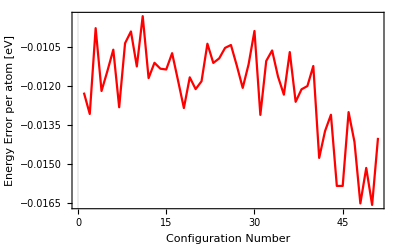

```mathematica
rmseTotenPlot=ListLinePlot[rmseTOTEN,
PlotRange->All,
PlotTheme->"Scientific" ,
(*GridLines->Automatic,*)
PlotStyle->Red,Frame->True,
Joined->True,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
FrameLabel->{"Configuration Number","Energy Error per atom [eV]"}]
```

```mathematica
Export[FileNameJoin[{figDir,"rmse-toten-plot.png"}], rmseTotenPlot, ImageResolution->300];
```

### RMSE FORCE

```mathematica
rmseForce=Import["ml_rmse_force.dat"];
```

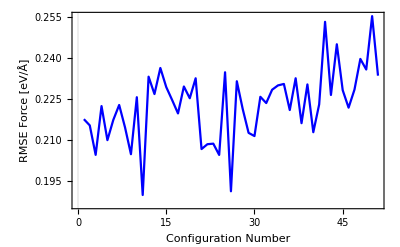

```mathematica
rmseForcePlot=ListLinePlot[rmseForce[[2;;]],
PlotRange->All,
PlotTheme->"Scientific" ,
(*GridLines->Automatic,*)
PlotStyle->Blue,Frame->True,
Joined->True,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
FrameLabel->{"Configuration Number","RMSE Force [eV/Å]"}]
```

```mathematica
Export[FileNameJoin[{figDir,"rmse-force-plot.png"}], rmseForcePlot, ImageResolution->300];
```

### RMSE STRESS

```mathematica
rmseStress=Import["rmse_stress.dat"][[2;;,All]];
```

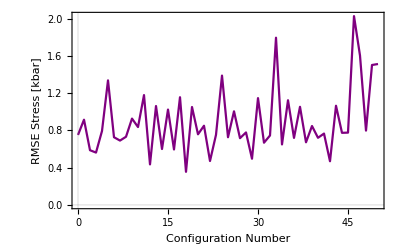

```mathematica
rmseStressPlot=ListLinePlot[rmseStress,
PlotRange->All,
PlotTheme->"Scientific" ,
(*GridLines->Automatic,*)
PlotStyle->Purple,Frame->True,
Joined->True,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
FrameLabel->{"Configuration Number","RMSE Stress [kbar]"}]
```

```mathematica
Export[FileNameJoin[{figDir,"rmse-stress-plot.png"}], rmseStressPlot, ImageResolution->300];
```

## Optimal Hyperparameters

### RCUT 1

```mathematica
rcut1Error=Import["rcut1/training_error.dat"];
```

```mathematica
(*Extract numerical data*)
rcut1Data=rcut1Error[[2;;43]];
```

```mathematica
(*Extract rcut values and each column*)
rcutValues1=rcut1Data[[All,1]];
energyValues1=rcut1Data[[All,2]];
forceValues1=rcut1Data[[All,3]];
stressValues1=rcut1Data[[All,4]];
```

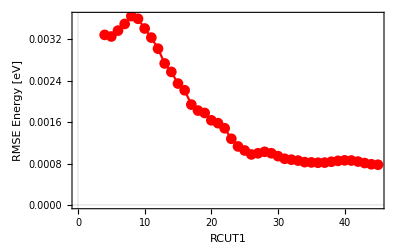

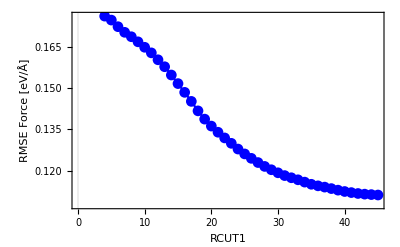

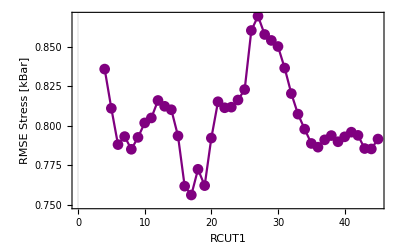

```mathematica
energyPlot1=
ListLinePlot[
Transpose[{rcutValues1,energyValues1}],
PlotMarkers->Automatic,
PlotStyle->Red,
Frame->True,
FrameLabel->{"RCUT1","RMSE Energy [eV]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific" 
];

forcePlot1=
ListLinePlot[Transpose[{rcutValues1,forceValues1}],
PlotMarkers->Automatic,
PlotStyle->Blue,
Frame->True,
FrameLabel->{"RCUT1","RMSE Force [eV/Å]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific"
];

stressPlot1=
ListLinePlot[Transpose[{rcutValues1,stressValues1}],
PlotMarkers->Automatic,
PlotStyle->Purple,
Frame->True,
FrameLabel->{"RCUT1","RMSE Stress [kBar]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific"
];

(*Show all plots separately*)
energyPlot1
forcePlot1
stressPlot1
```

```mathematica
Export[FileNameJoin[{figDir,"rcut-1-energy.png"}], energyPlot1, ImageResolution->300];
Export[FileNameJoin[{figDir,"rcut-1-force.png"}], forcePlot1, ImageResolution->300];
Export[FileNameJoin[{figDir,"rcut-1-stress.png"}], stressPlot1, ImageResolution->300];
```

### RCUT 2

```mathematica
rcut2Error=Import["rcut2/training_error.dat"];
```

```mathematica
(*Extract numerical data*)
rcut2Data=rcut2Error[[2;;]];
```

```mathematica
(*Extract rcut values and each column*)
rcutValues2=rcut2Data[[All,1]];
energyValues2=rcut2Data[[All,2]];
forceValues2=rcut2Data[[All,3]];
stressValues2=rcut2Data[[All,4]];
```

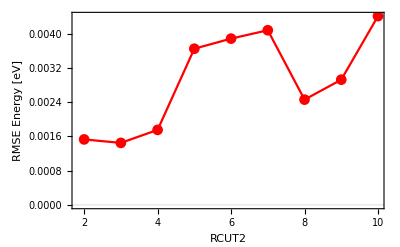

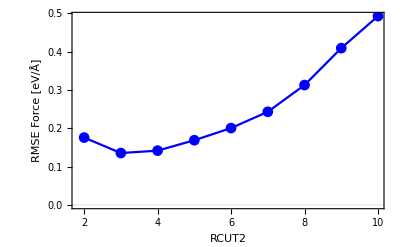

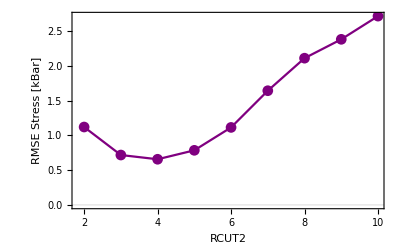

```mathematica
energyPlot2=
ListLinePlot[
Transpose[{rcutValues2,energyValues2}],
PlotMarkers->Automatic,
PlotStyle->Red,
Frame->True,
FrameLabel->{"RCUT2","RMSE Energy [eV]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific" 
];

forcePlot2=
ListLinePlot[Transpose[{rcutValues2,forceValues2}],
PlotMarkers->Automatic,
PlotStyle->Blue,
Frame->True,
FrameLabel->{"RCUT2","RMSE Force [eV/Å]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific" 
];

stressPlot2=
ListLinePlot[Transpose[{rcutValues2,stressValues2}],
PlotMarkers->Automatic,
PlotStyle->Purple,
Frame->True,
FrameLabel->{"RCUT2","RMSE Stress [kBar]"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
PlotTheme->"Scientific" 
];

(*Show all plots separately*)
energyPlot2
forcePlot2
stressPlot2
```

```mathematica
Export[FileNameJoin[{figDir,"rcut-2-energy.png"}], energyPlot2, ImageResolution->300];
Export[FileNameJoin[{figDir,"rcut-2-force.png"}], forcePlot2, ImageResolution->300];
Export[FileNameJoin[{figDir,"rcut-2-stress.png"}], stressPlot2, ImageResolution->300];
```

## RMSE Energy, Force & Stress (Refitted)

### TOTAL ENERGY

```mathematica
mlRFTOTEN=Import["ml_rf_data/ml_rf_toten.dat"];
```

```mathematica
rmseRFTOTEN= (mlRFTOTEN[[All,2]] - dtfTOTEN[[All,2]])/690;
```

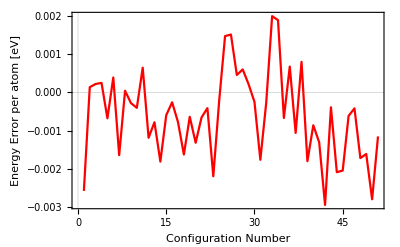

```mathematica
rmseRFTotenPlot=ListLinePlot[rmseRFTOTEN,
PlotRange->All,
PlotTheme->"Scientific" ,
(*GridLines->Automatic,*)
PlotStyle->Red,Frame->True,
Joined->True,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
FrameLabel->{"Configuration Number","Energy Error per atom [eV]"}]
```

```mathematica
Export[FileNameJoin[{figDir,"rmse-rf-toten-plot.png"}], rmseRFTotenPlot, ImageResolution->300];
```

### RMSE FORCE

```mathematica
rmseRFForce=Import["ml_rf_rmse_force.dat"];
```

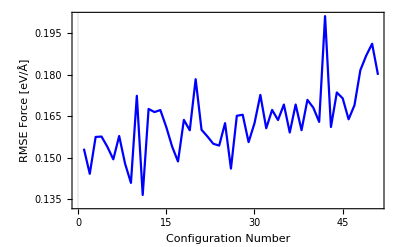

```mathematica
rmseRFForcePlot=ListLinePlot[rmseRFForce[[2;;]],
PlotRange->All,
PlotTheme->"Scientific" ,
(*GridLines->Automatic,*)
PlotStyle->Blue,Frame->True,
Joined->True,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
FrameLabel->{"Configuration Number","RMSE Force [eV/Å]"}]
```

```mathematica
Export[FileNameJoin[{figDir,"rmse-rf-force-plot.png"}], rmseRFForcePlot, ImageResolution->300];
```

### RMSE STRESS

```mathematica
rmseRFStress=Import["rmse_rf_stress.dat"][[2;;,All]];
```

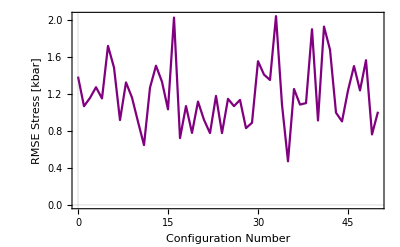

```mathematica
rmseRFStressPlot=ListLinePlot[rmseRFStress,
PlotRange->All,
PlotTheme->"Scientific" ,
(*GridLines->Automatic,*)
PlotStyle->Purple,Frame->True,
Joined->True,
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
FrameLabel->{"Configuration Number","RMSE Stress [kbar]"}]
```

```mathematica
Export[FileNameJoin[{figDir,"rmse-rf-stress-plot.png"}], rmseRFStressPlot, ImageResolution->300];
```

### Comparison

```mathematica
(*GraphicsRow[{rmseTotenPlot, rmseRFTotenPlot}]*)
```

```mathematica
(*GraphicsRow[{rmseForcePlot, rmseRFForcePlot}]*)
```

```mathematica
(*GraphicsRow[{rmseStressPlot, rmseRFStressPlot}]*)
```

## EOS

```mathematica
wrkdir = "/home/qbit/Documents/git-repositories/bachelor-thesis/cluster-files/ml-400k/eos/";
SetDirectory[wrkdir];
```

### EOS Model 1: RCUT1=36 & RCUT2=4

First try: use the volume of the last structure relaxed with ab initio

```mathematica
latt={{13.1833594583486668, 0.1844599657000000, 0.0075540083410000},{
-16.4524403008199727, 24.2162214736082717,-0.0087542302840000},
{1.2066498742698208,-0.8237562005712539, 23.1872985405888841}};
```

```mathematica
volume=(latt[[1]]×latt[[2]]).latt[[3]]
```

7472.73

This range corresponds to the first try for both models.

```mathematica
Range[volume (1-0.02),volume (1+0.02),20]//Map[ToString[NumberForm[#,{4,2}]]<>" "&,#]&//StringJoin
```

7323.00 7343.00 7363.00 7383.00 7403.00 7423.00 7443.00 7463.00 7483.00 7503.00 7523.00 7543.00 7563.00 7583.00 7603.00

```mathematica
Range[7023.00,7323.00,20]//Map[ToString[NumberForm[#,{4,2}]]<>" "&,#]&//StringJoin
```

7023.00 7043.00 7063.00 7083.00 7103.00 7123.00 7143.00 7163.00 7183.00 7203.00 7223.00 7243.00 7263.00 7283.00 7303.00 7323.00

Second try: Take the lowest energy structure based on the previous range, and generate a new range, with a smaller range and smaller step.

```mathematica
NewVol = 7303
```

7303

```mathematica
Range[NewVol,NewVol (1+0.01),10]//Map[ToString[NumberForm[#,{4,2}]]<>" "&,#]&//StringJoin
```

7303 7313 7323 7333 7343 7353 7363 7373

```mathematica
Range[NewVol,NewVol(1-0.01),-10]//Map[ToString[NumberForm[#,{4,2}]]<>" "&,#]&//StringJoin
```

7303 7293 7283 7273 7263 7253 7243 7233

Fig11 Model 1 using range 1

```mathematica
vol1Data1=Import["volume-m1.dat"];
```

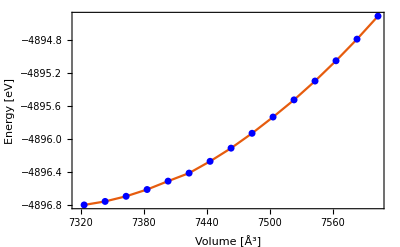

```mathematica
Fig11=vol1Data1//ListPlot[#,
PlotTheme->"Scientific",
(*GridLines->Automatic,*)
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Blue, AbsolutePointSize[5],
Point[#]}
]&
```

```mathematica
vol1Data2=Import["volume-m1-2.dat"];
```

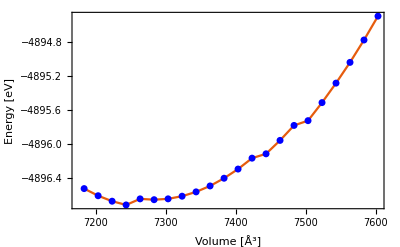

```mathematica
Fig12=vol1Data2//ListPlot[#,
PlotTheme->"Scientific",
(*GridLines->Automatic,*)
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Blue, AbsolutePointSize[5],
Point[#]}
]&
```

```mathematica
vol1Data3=Import["volume-m1-3.dat"];
```

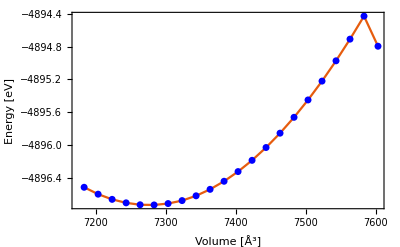

```mathematica
Fig13=vol1Data3//ListPlot[#,
PlotTheme->"Scientific",
(*GridLines->Automatic,*)
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Blue, AbsolutePointSize[5],
Point[#]}
]&
```

```mathematica
vol1Data4=Import["volume-m1-4.dat"];
```

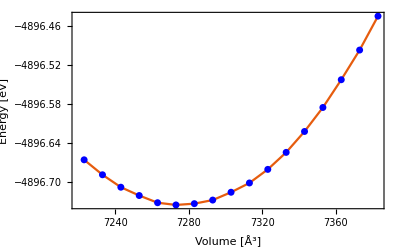

```mathematica
Fig14=vol1Data4//ListPlot[#,
PlotTheme->"Scientific",
(*GridLines->Automatic,*)
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Blue, AbsolutePointSize[5],
Point[#]}
]&
```

#### E0S

```mathematica
eos=e0+ (9 v0 B0)/16(((v0/v)^(2/3)-1)^3 B0'+((v0/v)^(2/3)-1)^2(6-4((v0/v)^(2/3))))
```

e0+9/16 B0 v0 ((6-4 (v0/v)^(2/3)) (-1+(v0/v)^(2/3))^2+(-1+(v0/v)^(2/3))^3 B0')

```mathematica
eos//PowerExpand//ExpandAll//Collect[#,v]&;
```

```mathematica
model = k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
parameters=Table[k[i],{i,4}]
```

{k[1],k[2],k[3],k[4]}

```mathematica
nlm1=NonlinearModelFit[vol1Data4,model,parameters,v]
```

FittedModel[…]

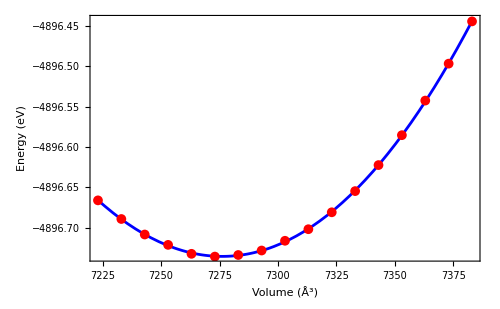

```mathematica
eosPlotM1=Plot[nlm1[v],{v,(vol1Data4[[All,1]]//Min)-0.2,(vol1Data4[[All,1]]//Max)+0.2},
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"Volume (Å^3)","Energy (eV)"},
PlotStyle->{AbsoluteThickness[2],Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[vol1Data4]}]
```

#### Bulk Modulus

```mathematica
nlm1["BestFitParameters"]
```

{k[1]→12917.3,k[2]→-1.89528×10^7,k[3]→6.69822×10^9,k[4]→-7.86006×10^11}

```mathematica
Sol1=Solve[{e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],
-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm1["BestFitParameters"],{e0,B0,v0,B'}]
```

{{e0→-4879.17,B0→-0.561701,v0→6031.27,B'→15.3389},{e0→-4896.74,B0→0.362538,v0→7276.16,B'→-6.0056}}

```mathematica
Sol1[[2,2,2]]//UnitConvert[Quantity[#,"Electronvolts"/("Angstroms")^3],"GigaPascals"]&
```

58.085 GPa

### EOS Model 2: RCUT1=17 & RCUT2=4

```mathematica
vol2Data1=Import["volume-m2.dat"];
```

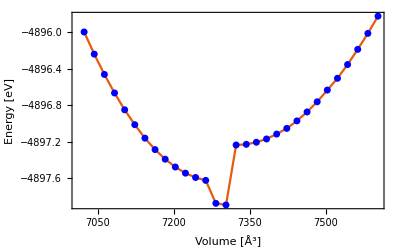

```mathematica
Fig21=vol2Data1//ListPlot[#,
PlotTheme->"Scientific",
(*GridLines->Automatic,*)
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Blue, AbsolutePointSize[5],
Point[#]}
]&
```

```mathematica
vol2Data2=Import["volume-m2-2.dat"];
```

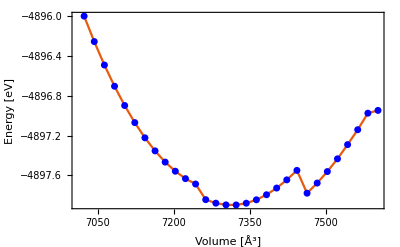

```mathematica
Fig22=vol2Data2//ListPlot[#,
PlotTheme->"Scientific",
(*GridLines->Automatic,*)
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Blue, AbsolutePointSize[5],
Point[#]}
]&
```

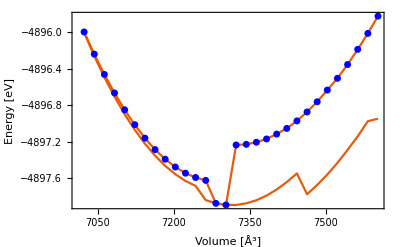

```mathematica
Show[Fig21, Fig22]
```

```mathematica
vol2Data3=Import["volume-m2-3.dat"];
```

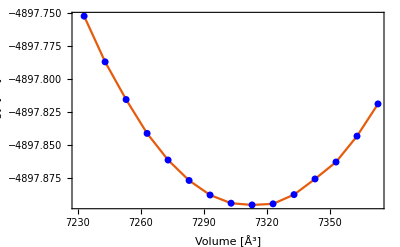

```mathematica
Fig23=vol2Data3//ListPlot[#,
PlotTheme->"Scientific",
(*GridLines->Automatic,*)
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Blue, AbsolutePointSize[5],
Point[#]}
]&
```

#### EOS

```mathematica
nlm2=NonlinearModelFit[vol2Data3,model,parameters,v]
```

FittedModel[…]

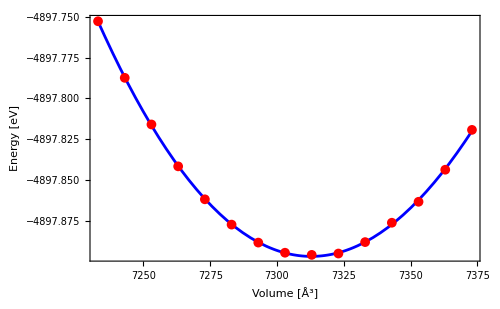

```mathematica
eosPlotM2=Plot[nlm2[v],{v,(vol2Data3[[All,1]]//Min)-0.2,(vol2Data3[[All,1]]//Max)+0.2},
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]"},
PlotStyle->{AbsoluteThickness[2],Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[vol2Data3]}]
```

```mathematica
Export[FileNameJoin[{figDir,"eos-m2.png"}], eosPlotM2, ImageResolution->300];
```

#### Bulk Modulus

```mathematica
nlm2["BestFitParameters"]
```

{k[1]→-8209.05,k[2]→4.73019×10^6,k[3]→-2.15425×10^9,k[4]→3.17274×10^11}

```mathematica
Sol2=Solve[{e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],
-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm2["BestFitParameters"],{e0,B0,v0,B'}];
```

```mathematica
bulk2=Sol2[[1,2,2]]//UnitConvert[Quantity[#,"Electronvolts"/("Angstroms")^3],"GigaPascals"]&
```

51.0563 GPa

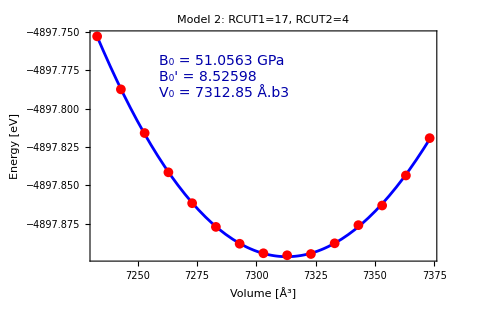

```mathematica
Plot[nlm2[v],
{v,(vol2Data3[[All,1]]//Min)-0.2,
(vol2Data3[[All,1]]//Max)+0.2},
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]"},
PlotStyle->{AbsoluteThickness[2],Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
PlotLabel->Style["Model 2: RCUT1=17, RCUT2=4",18],Epilog->{AbsolutePointSize[7],Red,Point[vol2Data3],Inset[Style[Row[{"B_0 = ",bulk2,"\n","B_0' = ",Sol2[[1,4,2]],"\n","V₀ = ",Sol2[[1,3,2]]," Å.b3"}],FontSize->14,FontFamily->"Times", FontColor->Darker@Blue],Scaled[{0.2,0.9}],{Left,Top}]}]
```

## Simulated Annealing EOS

```mathematica
wrkdir = "/home/qbit/Documents/git-repositories/bachelor-thesis/cluster-files/ml-400k/eos-sa/";
SetDirectory[wrkdir];
```

```mathematica
vol1SaDat1 = Import["volume-sa-1.dat"]
```

{{7203.,-4908.95},{7223.,-4909.1},{7243.,-4909.23},{7263.,-4909.33},{7283.,-4909.41},{7303.,-4909.48},{7323.,-4909.52},{7343.,-4909.54},{7363.,-4909.54},{7383.,-4909.53},{7403.,-4909.5},{7423.,-4909.44},{7443.,-4909.37},{7463.,-4909.28},{7483.,-4909.17},{7503.,-4909.09},{7523.,-4908.95},{7543.,-4908.8},{7563.,-4908.63},{7583.,-4908.45},{7603.,-4908.28}}

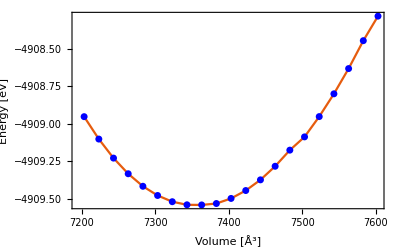

```mathematica
vol1SaPlot=vol1SaDat1//ListPlot[#,
PlotTheme->"Scientific",
(*GridLines->Automatic,*)
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Blue, AbsolutePointSize[5],
Point[#]}
]&
```

### EOS

```mathematica
nlmSA1=NonlinearModelFit[vol1SaDat1,model,parameters,v]
```

FittedModel[…]

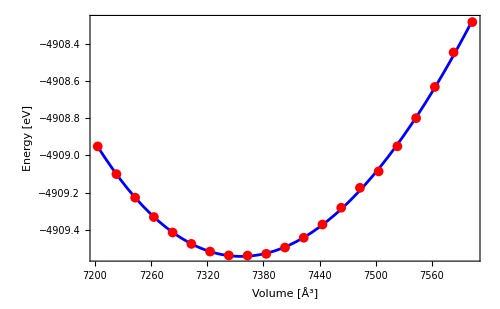

```mathematica
eosPlotSian=Plot[nlmSA1[v],{v,(vol1SaDat1[[All,1]]//Min)-0.2,(vol1SaDat1[[All,1]]//Max)+0.2},
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]"},
PlotStyle->{AbsoluteThickness[2],Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[vol1SaDat1]}]
```

```mathematica
Export[FileNameJoin[{figDir,"eos-sian.png"}], eosPlotSian, ImageResolution->300];
```

#### Bulk Modulus

```mathematica
nlmSA1["BestFitParameters"]
```

{k[1]→-10045.1,k[2]→6.9042×10^6,k[3]→-3.01873×10^9,k[4]→4.31951×10^11}

```mathematica
SolSa1=Solve[{e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],
-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlmSA1["BestFitParameters"],{e0,B0,v0,B'}]
```

{{e0→-4909.54,B0→0.344022,v0→7356.09,B'→9.60769},{e0→-4855.89,B0→-0.133012,v0→11053.9,B'→-0.274361}}

```mathematica
bulkSa1=SolSa1[[1,2,2]]//UnitConvert[Quantity[#,"Electronvolts"/("Angstroms")^3],"GigaPascals"]&
```

55.1185 GPa

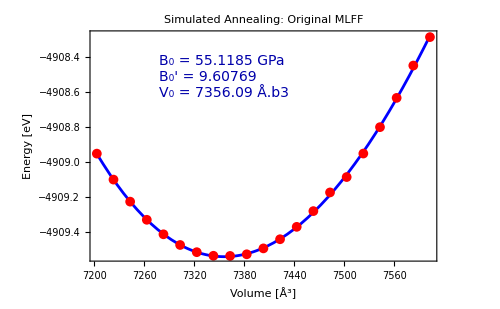

```mathematica
Plot[nlmSA1[v],
{v,(vol1SaDat1[[All,1]]//Min)-0.2,
(vol1SaDat1[[All,1]]//Max)+0.2},
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]"},
PlotStyle->{AbsoluteThickness[2],Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
PlotLabel->Style["Simulated Annealing: Original MLFF",18],Epilog->{AbsolutePointSize[7],Red,Point[vol1SaDat1],Inset[Style[Row[{"B_0 = ",bulkSa1,"\n","B_0' = ",SolSa1[[1,4,2]],"\n","V₀ = ",SolSa1[[1,3,2]]," Å.b3"}],FontSize->14,FontFamily->"Times", FontColor->Darker@Blue],Scaled[{0.2,0.9}],{Left,Top}]}]
```

### Comparison

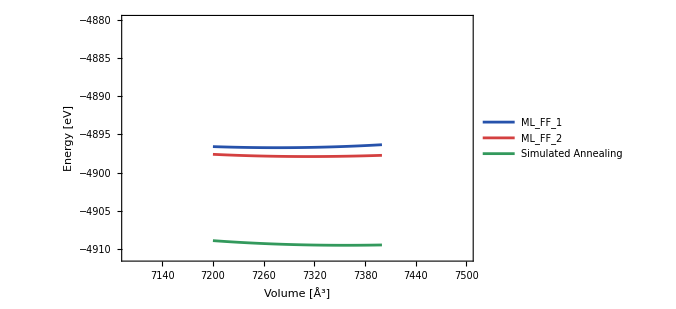

```mathematica
Plot[{nlm1[v], nlm2[v], nlmSA1[v]},{v,7200.0,7400.0},
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]"},
PlotStyle->{
{RGBColor[0.15,0.32,0.67],AbsoluteThickness[2]},{RGBColor[0.83,0.25,0.25],AbsoluteThickness[2]},{RGBColor[0.20,0.60,0.36],AbsoluteThickness[2]}
},
PlotLegends->{"ML_FF_1","ML_FF_2","Simulated Annealing"},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->{{7100,7500},{-4911,-4880}}]
```

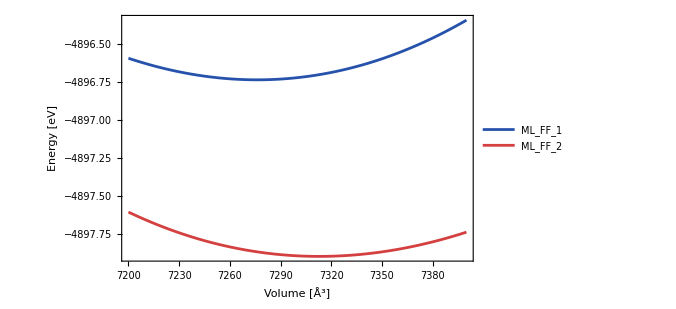

```mathematica
Plot[{nlm1[v], nlm2[v]},{v,7200.0,7400.0},
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]"},
PlotStyle->{
{RGBColor[0.15,0.32,0.67],AbsoluteThickness[2]},{RGBColor[0.83,0.25,0.25],AbsoluteThickness[2]}
},
PlotLegends->{"ML_FF_1","ML_FF_2"},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All]
```

## Simulated Annealing EOS

```mathematica
wrkdir = "/home/qbit/Documents/git-repositories/bachelor-thesis/cluster-files/ml-400k/eos-sa/";
SetDirectory[wrkdir];
```

```mathematica
vol1SaDat1 = Import["volume-sa-2.dat"]
```

{{7233.,-4909.17},{7243.,-4909.23},{7253.,-4909.28},{7263.,-4909.33},{7273.,-4909.38},{7283.,-4909.41},{7293.,-4909.45},{7303.,-4909.48},{7313.,-4909.5},{7323.,-4909.52},{7333.,-4909.53},{7343.,-4909.54},{7353.,-4909.54},{7363.,-4909.54},{7373.,-4909.54},{7383.,-4909.53},{7393.,-4909.51},{7403.,-4909.5},{7413.,-4909.47},{7423.,-4909.44},{7433.,-4909.41},{7443.,-4909.37}}

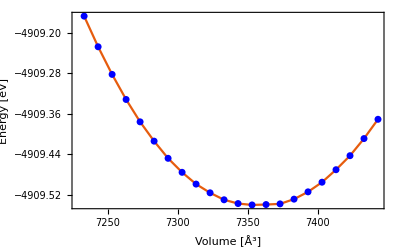

```mathematica
vol1SaPlot=vol1SaDat1//ListPlot[#,
PlotTheme->"Scientific",
(*GridLines->Automatic,*)
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Blue, AbsolutePointSize[5],
Point[#]}
]&
```

### EOS

```mathematica
nlmSA1=NonlinearModelFit[vol1SaDat1,model,parameters,v]
```

FittedModel[…]

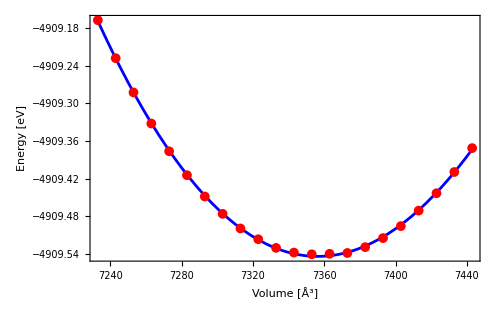

```mathematica
eosPlotSian=Plot[nlmSA1[v],{v,(vol1SaDat1[[All,1]]//Min)-0.2,(vol1SaDat1[[All,1]]//Max)+0.2},
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]"},
PlotStyle->{AbsoluteThickness[2],Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[vol1SaDat1]}]
```

```mathematica
Export[FileNameJoin[{figDir,"eos-sian.png"}], eosPlotSian, ImageResolution->300];
```

#### Bulk Modulus

```mathematica
nlmSA1["BestFitParameters"]
```

{k[1]→-7028.99,k[2]→3.48718×10^6,k[3]→-1.72834×10^9,k[4]→2.69522×10^11}

```mathematica
SolSa1=Solve[{e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],
-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlmSA1["BestFitParameters"],{e0,B0,v0,B'}]
```

{{e0→-4909.54,B0→0.345698,v0→7356.38,B'→7.48163},{e0→-4769.68,B0→-0.063795,v0→15177.4,B'→1.8517}}

```mathematica
bulkSa1=SolSa1[[1,2,2]]//UnitConvert[Quantity[#,"Electronvolts"/("Angstroms")^3],"GigaPascals"]&
```

55.3869 GPa

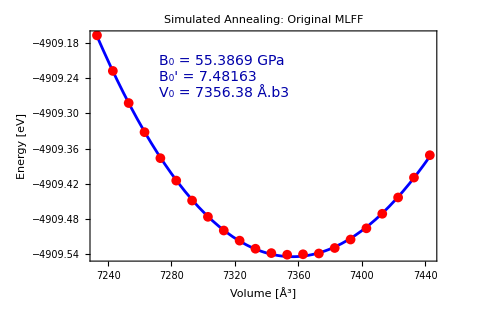

```mathematica
Plot[nlmSA1[v],
{v,(vol1SaDat1[[All,1]]//Min)-0.2,
(vol1SaDat1[[All,1]]//Max)+0.2},
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]"},
PlotStyle->{AbsoluteThickness[2],Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
PlotLabel->Style["Simulated Annealing: Original MLFF",18],Epilog->{AbsolutePointSize[7],Red,Point[vol1SaDat1],Inset[Style[Row[{"B_0 = ",bulkSa1,"\n","B_0' = ",SolSa1[[1,4,2]],"\n","V₀ = ",SolSa1[[1,3,2]]," Å.b3"}],FontSize->14,FontFamily->"Times", FontColor->Darker@Blue],Scaled[{0.2,0.9}],{Left,Top}]}]
```

### Comparison

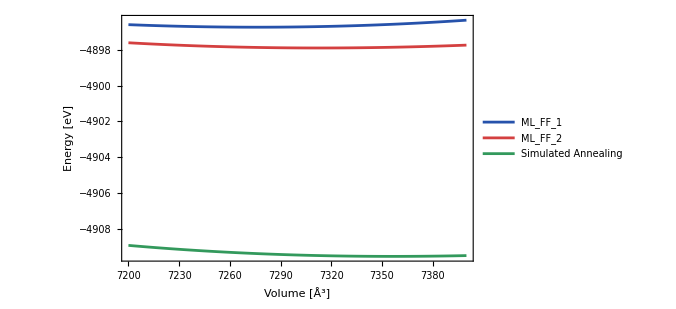

```mathematica
Plot[{nlm1[v], nlm2[v], nlmSA1[v]},{v,7200.0,7400.0},
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]"},
PlotStyle->{
{RGBColor[0.15,0.32,0.67],AbsoluteThickness[2]},{RGBColor[0.83,0.25,0.25],AbsoluteThickness[2]},{RGBColor[0.20,0.60,0.36],AbsoluteThickness[2]}
},
PlotLegends->{"ML_FF_1","ML_FF_2","Simulated Annealing"},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All]
```

```mathematica
Plot[{nlm1[v], nlm2[v]},{v,7200.0,7400.0},
PlotTheme->"Scientific",
Frame->True,
FrameLabel->{"Volume [Å^3]","Energy [eV]"},
PlotStyle->{
{RGBColor[0.15,0.32,0.67],AbsoluteThickness[2]},{RGBColor[0.83,0.25,0.25],AbsoluteThickness[2]}
},
PlotLegends->{"ML_FF_1","ML_FF_2"},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All]
```

-Graphics-